```mathematica
Code20InterpRow=FunctionCompile[Function[Typed[init, "PackedArray"::["MachineReal", 1]], With[{padded=Join[{0., 0.}, init, {0., 0.}]},Table[With[{sum=Total[padded[[i;;i+4]]]}, With[{o=Which[sum>=3.,1.-Abs[sum-4.], sum>=1., 1.-Abs[sum-2.],True, 0.]}, 0.6o+0.4o*o]], {i, Length[init]}]]],CompilerOptions->{"LLVMOptimization"->"ClangOptimization"[3],"OptimizationLevel"->3}];
```

```mathematica
Code20InterpRow[{1, 0, 1, 1, 1, 1, 0, 1}+.01RandomReal[{0,1}, 8]]//Round
```

{1,0,1,1,1,1,0,1}

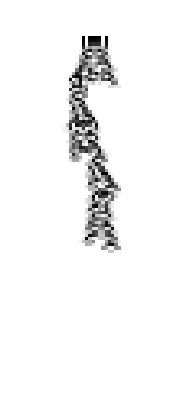

```mathematica
ArrayPlot[NestList[Code20InterpRow, ArrayPad[{1, 0, 1, 1, 1, 1, 0, 1}+.01RandomReal[{0,1}, 8], 20], 100]]
```

```mathematica
First[RepeatedTiming[Code20InterpRow[RandomReal[{0, 1}, 100]]]]
```

0.0000187549

```mathematica
GrayCode=ResourceFunction["GrayCode"];
GrayCodeList[l_List]:=With[{gc=GrayCode[l]}, {maxlen=Max[Length/@gc]},PadLeft[#, maxlen]&/@gc]
```

```mathematica
numBits=10;
gci=Interpolation[Transpose[{Range[0, 2^numBits-1], GrayCodeList[Range[0, 2^numBits-1]]}], InterpolationOrder->1];
```

```mathematica
NumericQ
```

NumericQ

```mathematica
Clear[f]
f[x_?NumericQ]:=If[0<=x&&x<=2^numBits-1,Total[Nest[Code20InterpRow,gci[x],50]], 0]

NMaximize[f[x], {x}]
```

{4.00427,{x→4.01987}}

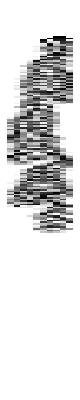

```mathematica
ArrayPlot[NestList[Code20InterpRow,gci[x/.Last[]], 200]]
```

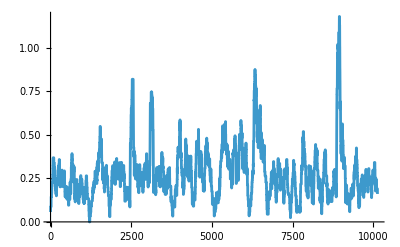

```mathematica
ListLinePlot[MovingAverage[Table[f[x], {x, 0, 2^numBits-1, 0.1}], 100], PlotRange->All]
```